```mathematica
Dpdf[a_,h_,Rm_,mu_,d_,c_]:=Piecewise[{{Sin[(a+c*h)/Rm],d<c*h},{Sin[(a+d)/Rm]*((d/(c*h))^-(3*mu/2+1)+10^-3),d≥c*h}}]
```

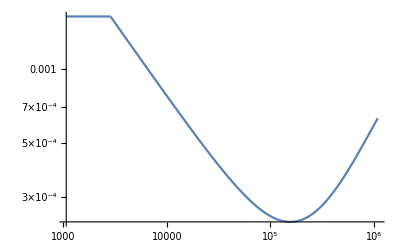

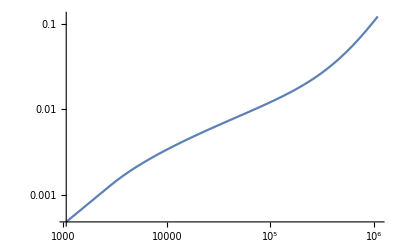

```mathematica
Rmm=1737000;
aa=4.5;
hh=50;
LogLogPlot[Dpdf[aa,hh,Rmm,0.4,d,57],{d,0,Rmm*Pi/5-aa}]
LogLogPlot[NIntegrate[Dpdf[aa,hh,Rmm,0.4,x,57],{x,0,d}]/NIntegrate[Dpdf[aa,hh,Rmm,0.4,x,57],{x,0,Rmm*Pi-aa}],{d,0,Rmm*Pi/5-aa}]
```